```mathematica
FullSimplify@Integrate[ 1/t,{t,1,x}]
```

ConditionalExpression[Log[x],Re[x]≥0||x∉Reals]

```mathematica
FullSimplify@Integrate[1/(-1+t)-ⅇ^(1-t)/(-1+t),{t,1,x}]
```

ConditionalExpression[EulerGamma+Gamma[0,-1+x]+Log[-1+x],Re[x]>1]

```mathematica
FullSimplify@Integrate[1/Log[t]-1/(t Log[t]),{t,1,x}]
```

ConditionalExpression[-EulerGamma-Gamma[0,-Log[x]]-Log[-Log[x]],Im[x]≠0||Re[x]≥0]

```mathematica
N[Integrate[(1/(-1+t)-ⅇ^(1-t)/(-1+t))(1/(-1+u)-ⅇ^(1-u)/(-1+u)),{t,0,x},{u,0,x-t}]/.x->9.]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {8.01549}. NIntegrate obtained 13.6164  + 24.1341\ ⅈ
 and 0.000625121 for the integral and error estimates.

13.6164+24.1341 ⅈ

```mathematica
N[D[LaguerreL[z,1-(10)],{z,2}]/.z->0]
```

6.28971

```mathematica
N[Integrate[(1/(-1+t)-ⅇ^(1-t)/(-1+t))(1/(-1+u)-ⅇ^(1-u)/(-1+u)),{t,0,x},{u,1,x-t}]/.x->10.]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {9.00375}. NIntegrate obtained 15.9202  - 12.4868\ ⅈ
 and 0.000495532 for the integral and error estimates.

15.9202-12.4868 ⅈ

```mathematica
Sum[ x^k/k! N[D[Pochhammer[n,z]/z!,{z,k}]/.z->0/.n->12],{k,0,16}]/.x->-2.2+3I
```

-1.11018-0.1562 ⅈ

```mathematica
{N[D[Pochhammer[n+1,z]/z!,{z,2}]/.n->6/.z->0],N@Sum[ 1/j 1/k,{j,1,6},{k,1,6-j}]}
```

{4.51111,4.51111}

```mathematica
{N[D[Pochhammer[n+1,z]/z!,{z,1}]/.n->6/.z->0],N@Sum[ 1/j,{j,1,6}]}
```

{2.45,2.45}

```mathematica
{N[D[Pochhammer[z+1,n]/n!,{z,2}]/.n->6/.z->0],N@Sum[ 1/j 1/k,{j,1,6},{k,1,6-j}]}
```

{4.51111,4.51111}

```mathematica
{N[D[Pochhammer[n,z]/z!,{z,3}]/.n->17/.z->0],N@Sum[ 1/j 1/k 1/l,{j,1,16},{k,1,16-j},{l,1,16-j-k}]}
```

{24.9712,24.9712}

```mathematica
{N[Integrate[ (1/Log[x]-1/(x Log[x]))(1/Log[y]-1/(y Log[y])),{x,1,n},{y,1,n/x}]/.n->7],N[D[LaguerreL[-z,Log[n]],{z,2}]/.z->0/.n->7]}
```

{3.93891,3.93891}

```mathematica
{N[Integrate[ ((x-1)/(x Log[x]))((y-1)/(y Log[y])),{x,1,n},{y,1,n/x}]/.n->7],N[D[LaguerreL[-z,Log[n]],{z,2}]/.z->0/.n->7]}
```

{3.93891,3.93891}

```mathematica
{N[D[LaguerreL[z,1-7],z]/.z->0],N[Integrate[1/(-1+t)-ⅇ^(1-t)/(-1+t),{t,1,7}]]}
```

{2.36934,2.36934}

```mathematica
{N[D[LaguerreL[z,1-8],{z,2}]/.z->0],N[Integrate[(1/(-1+t)-ⅇ^(1-t)/(-1+t))(1/(-1+u)-ⅇ^(1-u)/(-1+u)),{t,1,8},{u,1,8-t+1}]]}
```

{5.03314,5.03314-7.927 ⅈ}

```mathematica
D[EulerGamma+Gamma[0,-1+x]+Log[-1+x],x]
```

1/(-1+x)-ⅇ^(1-x)/(-1+x)

```mathematica
D[EulerGamma+Gamma[0,x]+Log[x],x]
```

1/x-ⅇ^-x/x

```mathematica
Integrate[ 1/x-ⅇ^-x/x,{x,0,n-1}]
```

ConditionalExpression[EulerGamma+Gamma[0,-1+n]+Log[-1+n],Re[n]>1]

```mathematica
1/x-ⅇ^-x/x/.x->t
```

1/t-ⅇ^-t/t

```mathematica
1/x-ⅇ^-x/x/.x->u
```

1/u-ⅇ^-u/u

```mathematica
{N[D[LaguerreL[z,-7],z]/.z->0],N[Integrate[(1/t-ⅇ^-t/t),{t,0,7}]]}
```

{2.52324,2.52324}

```mathematica
{N[D[LaguerreL[z,-7],{z,2}]/.z->0],N[Integrate[(1/t-ⅇ^-t/t)(1/u-ⅇ^-u/u),{t,0,7},{u,0,7-t}]]}
```

{5.03314,5.03314}

```mathematica
{N[D[LaguerreL[z,-7],{z,3}]/.z->0],N[Integrate[(1/t-ⅇ^-t/t)(1/u-ⅇ^-u/u)(1/v-ⅇ^-v/v),{t,0,7},{u,0,7-t},{v,0,7-t-u}]]}
```

{8.19258,8.19258}

```mathematica
pr[n_,z_]:=Pochhammer[n+1,z]/z!
pr2[n_,z_]:=(n+z)!/(n!z!)
pr2a[n_,z_]:=1/Beta[n+1,z+1]/(n+z+1)
```

```mathematica
{N[D[pr2[n,z],{z,2}]/.n->6/.z->0],N@Sum[ 1/j 1/k,{j,1,6},{k,1,6-j}]}
```

{4.51111,4.51111}

```mathematica
{N[D[pr2[n,z],{z,3}]/.n->6/.z->0],N@Sum[ 1/j 1/k 1/l,{j,1,6},{k,1,6-j},{l,1,6-j-k}]}
```

{6.125,6.125}

```mathematica
FullSimplify[Integrate[ (1-E^(-t))/(t),{t,0,n}]]
```

ConditionalExpression[EulerGamma+Gamma[0,n]+Log[n],Re[n]>0]

```mathematica
Clear[F,G,G2]
F[n_,j_,k_,z_,d_]:=F[n,j,k,z,d]=If[n<j,0,d((z+1)/k-1)(1+F[Floor[n/j],1+d,k+1,z,d])+F[n,j+1,k,z,d]]
zetaalt[n_,z_,d_]:=1+F[n,1+d,1,z,d]
G[n_,j_,k_,z_,d_]:=G[n,j,k,z,d]=If[n<j,0,d((z+1)/k-1)(1+G[n-j,d,k+1,z,d])+G[n,j+1,k,z,d]]
betaalt[n_,z_,d_]:=1+G[n,d,1,z,d]
G2[n_,j_,k_,z_,d_]:=G2[n,j,k,z,d]=If[n<j,0,(-1)^(j+1)d((z+1)/k-1)(1+G2[n-j,d,k+1,z,d])+G2[n,j+1,k,z,d]]
beta2alt[n_,z_,d_]:=1+G2[n,d,1,z,d]
```

```mathematica
Expand@zetaalt[100,z,1]
```

1+(428 z)/15+(16289 z^2)/360+(331 z^3)/16+(611 z^4)/144+(67 z^5)/240+(7 z^6)/720

```mathematica
Expand@betaalt[10,z,1]
```

1+(7381 z)/2520+(177133 z^2)/50400+(84095 z^3)/36288+(341693 z^4)/362880+(8591 z^5)/34560+(7513 z^6)/172800+(121 z^7)/24192+(11 z^8)/30240+(11 z^9)/725760+z^10/3628800

```mathematica
Expand@FullSimplify@Sum[(D[pr[10,z],{z,k}]/.z->0)z^k/k!,{k,0,10}]
```

1+(7381 z)/2520+(177133 z^2)/50400+(84095 z^3)/36288+(341693 z^4)/362880+(8591 z^5)/34560+(7513 z^6)/172800+(121 z^7)/24192+(11 z^8)/30240+(11 z^9)/725760+z^10/3628800

```mathematica
N@Expand@betaalt[10,z]/.z->-1.5
```

-0.00927353

```mathematica
pr2[10,-1.5]
```

-0.00927353

```mathematica
N@Sum[(D[pr[10,z],{z,k}]/.z->0)z^k/k!,{k,0,10}]/.z->-1.5
```

-0.00927353

```mathematica
Expand@betaalt[10,z,1]
```

1+(7381 z)/2520+(177133 z^2)/50400+(84095 z^3)/36288+(341693 z^4)/362880+(8591 z^5)/34560+(7513 z^6)/172800+(121 z^7)/24192+(11 z^8)/30240+(11 z^9)/725760+z^10/3628800

```mathematica
Clear[s2o,sa2o]
bin[z_,k_]:=Product[z-j,{j,0,k-1}]/k!
s2o[n_,0]:=UnitStep[n]
s2o[n_,k_]:=s2o[n,k]=Sum[  (-1)^(j)s2o[n-j,k-1],{j,1,n}]
sz2[n_,z_]:=Sum[ bin[z,k]s2o[n,k],{k,0,n}]
sa2o[n_,0]:=UnitStep[n]
sa2o[n_,k_]:=sa2o[n,k]=Sum[  sa2o[n-j,k-1],{j,1,n}]
saz2[n_,z_]:=Sum[ bin[z,k]sa2o[n,k],{k,0,n}]
```

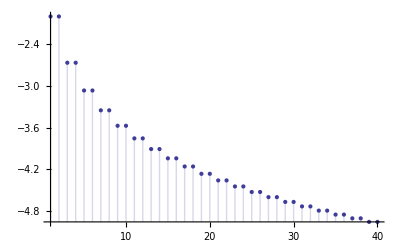

```mathematica
DiscretePlot[D[sz2[n,z]-saz2[n,z],z]/.z->0,{n,1,40}]
```

```mathematica
N@Log[1/2]
```

-0.693147

```mathematica
N@Integrate[1/(j!),{j,0,Infinity}]
```

2.26653

```mathematica
N@Integrate[1/(j!) 1/(k!),{j,0,Infinity},{k,0,Infinity}]
```

5.13718

```mathematica
N@Integrate[1/(j!) 1/(k!) 1/(l!),{j,0,Infinity},{k,0,Infinity},{l,0,Infinity}]
```

11.6436

```mathematica
N@Sum[1/(j!),{j,0,Infinity}]
```

2.71828

```mathematica
N@Sum[1/(j!) 1/(k!),{j,0,Infinity},{k,0,Infinity}]
```

7.38906

```mathematica
N[D[Sum[ z^k/(k!),{k,0,n}],{z,1}]/.z->0/.n->10]
```

1.

```mathematica
D[Integrate[ z^k/k!,{k,0,n}],z]/.z->0
```

∫_0^n (0^(-1+k) k)/(k!)ⅆk

```mathematica
D[Sum[ z^k/k!,{k,0,10}],z]/.z->0
```

1